### Problema 1

```mathematica
k1=50;
```

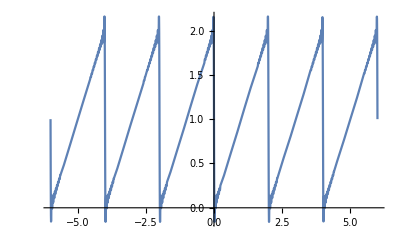

```mathematica
Plot[1+Sum[I/(n Pi)Exp[I n Pi t],{n,-k1,-1}]+Sum[I/(n Pi)Exp[I n Pi t],{n,1,k1}],{t,-6,6}]
```

### Pregunta 2

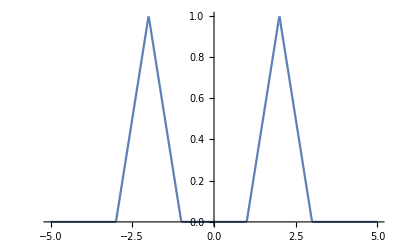

```mathematica
Plot[(w+3)(UnitStep[w+3]-UnitStep[w+2]) + (-(w+1))(UnitStep[w+2]-UnitStep[w+1])+
(w-1)(UnitStep[w-1]-UnitStep[w-2])+(-w+3)(UnitStep[w-2]-UnitStep[w-3]),{w,-5,5}]
```

```mathematica
InverseFourierTransform[ (w+3)(UnitStep[w+3]-UnitStep[w+2]) + (-(w+1))(UnitStep[w+2]-UnitStep[w+1])+
(w-1)(UnitStep[w-1]-UnitStep[w-2])+(-w+3)(UnitStep[w-2]-UnitStep[w-3]),w,t ,FourierParameters->{1,-1}]
```

-ⅇ^(-ⅈ t)/(2 π t^2)-ⅇ^(ⅈ t)/(2 π t^2)+ⅇ^(-2 ⅈ t)/(π t^2)+ⅇ^(2 ⅈ t)/(π t^2)-ⅇ^(-3 ⅈ t)/(2 π t^2)-ⅇ^(3 ⅈ t)/(2 π t^2)

```mathematica
ExpToTrig[-ⅇ^(-ⅈ t)/(2 π t^2)-ⅇ^(ⅈ t)/(2 π t^2)+ⅇ^(-2 ⅈ t)/(π t^2)+ⅇ^(2 ⅈ t)/(π t^2)-ⅇ^(-3 ⅈ t)/(2 π t^2)-ⅇ^(3 ⅈ t)/(2 π t^2)]
```

-Cos[t]/(π t^2)+(2 Cos[2 t])/(π t^2)-Cos[3 t]/(π t^2)

### Pregunta 4

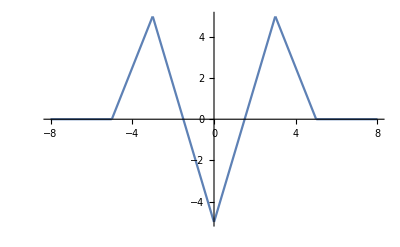

```mathematica
Plot[(5/2(t+5))(UnitStep[t+5]-UnitStep[t+3])+(-5-10/3 t)(UnitStep[t+3]-UnitStep[t])+
(-5+10/3 t)(UnitStep[t]-UnitStep[t-3])+(-5/2(t-5))(UnitStep[t-3]-UnitStep[t-5]),{t,-8,8}]
```

```mathematica
FourierTransform[(5/2(t+5))(UnitStep[t+5]-UnitStep[t+3])+(-5-10/3 t)(UnitStep[t+3]-UnitStep[t])+
(-5+10/3 t)(UnitStep[t]-UnitStep[t-3])+(-5/2(t-5))(UnitStep[t-3]-UnitStep[t-5]),t,w,FourierParameters->{1,-1}]
```

-20/(3 w^2)+(35 Cos[3 w])/(3 w^2)-(5 Cos[5 w])/w^2

```mathematica
Integrate[((5/2(t+5))(UnitStep[t+5]-UnitStep[t+3])+(-5-10/3 t)(UnitStep[t+3]-UnitStep[t])+
(-5+10/3 t)(UnitStep[t]-UnitStep[t-3])+(-5/2(t-5))(UnitStep[t-3]-UnitStep[t-5]))^2,{t,-10,10}]
```

250/3

### Pregunta 5

```mathematica
FourierTransform[Exp[-8 t] UnitStep[t],t,w,FourierParameters->{1,-1}]
```

-ⅈ/(-8 ⅈ+w)

```mathematica
Integrate[1/(8^2+w^2),{w,-Infinity,Infinity}]
```

π/8

```mathematica
Integrate[1/(8^2+w^2),{w,-Infinity,-10}]+Integrate[1/(8^2+w^2),{w,10,Infinity}]
```

1/8 (π-2 ArcTan[5/4])

```mathematica
A =√(3/4*Integrate[1/(8^2+w^2),{w,-Infinity,Infinity}]/(Integrate[1/(8^2+w^2),{w,-Infinity,-10}]+Integrate[1/(8^2+w^2),{w,10,Infinity}]))
```

1/2 √((3 π)/(π-2 ArcTan[5/4]))

```mathematica
N[A]
```

1.32136